```mathematica
Int1=2/(a^3*R)(Integrate[Exp[(-2r)/a]r(r+R),{r,0,Infinity}]-Integrate[Exp[(-2r)/a]r(R-r),{r,0,R}]-Integrate[Exp[(-2r)/a]r(r-R),{r,R,Infinity}]);
Int2=1/(2R b^2)(Integrate[Exp[-2/b(R-r)](b+2(R-r)),{r,0,R}]+Integrate[Exp[-2/b(r-R)](b+2(r-R)),{r,R,Infinity}]-Integrate[Exp[-2/b(R+r)](2(r+R)+b),{r,0,Infinity}]);
Int3=(2b)/(R(a b)^(3/2))(Integrate[Exp[-R/b+r(1/b-1/a)]r,{r,0,R}]+Integrate[Exp[R/b-r(1/a+1/b)]r,{r,R,Infinity}]-Integrate[Exp[-R/b-r(1/a+1/b)],{r,0,Infinity}]);
Sab=(2b)/(R(a b)^(3/2))(Integrate[Exp[-r/a]Exp[(r-R)/b]r(b+R-r),{r,0,R}]+Integrate[Exp[-r/a]Exp[(R-r)/b]r(b+r-R),{r,R,Infinity}]-Integrate[Exp[-r/a]Exp[-(r+R)/b]r(b+r+R),{r,0,Infinity}]);
```

```mathematica
(*Eab es la expresión para la energía en términos de a y b:*)
Eab=(-Za^2/2-Zb(Int1)+C1^2(-Zb^2/2-Za(Int2))+2C1(-Za^2/2 Sab-Zb (Int3)))/(1+C1^2+2C1 Sab)+(Za*Zb)/R;
```

```mathematica
(*Para obtener la gráfica del Griffiths (Za=Zb=1) debemos tomar dos límites: Zb->Za y b->a y luego hacemos unas sustituciones para volverla función de x*)
FullSimplify[Limit[Limit[Eab,Zb->Za],b->a] /.{R/a->x,a->1/Za,R->x/Za}]
```

ConditionalExpression[(ⅇ^-x Za^2 (6 (1+C1^2) (1+x)-3 (1+C1^2) ⅇ^(2 x) (2+x-2 Za)-2 C1 ⅇ^x (3+9 x+9 x^2+x^3-2 (6+x (3+x)) Za)))/(2 x (3 (1+C1^2) ⅇ^x+2 C1 (3+x (3+x)))), Re[1/Za]>0]

#### Físicamente, entiendo lo anterior como aproximar la carga del núcleo Z_a=1 y Z_b=1 entre sí hasta formar la molécula H_2^+:

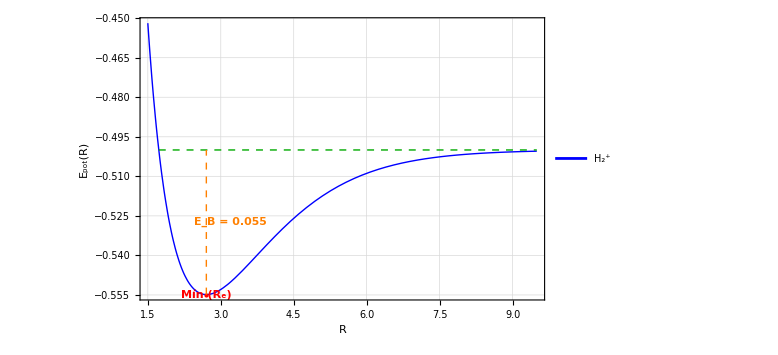

```mathematica
(* ===Definición del potencial homogéneo===*)Ex[x_,Za_,C1_]:=(E^-x Za^2 (6 (1+C1^2) (1+x)-3 (1+C1^2) E^(2 x) (2+x-2 Za)-2 C1 E^x (3+9 x+9 x^2+x^3-2 (6+x (3+x)) Za)))/(2 x (3 (1+C1^2) E^x+2 C1 (3+x (3+x))));
(* ===Encontrar mínimo de la función===*)
min=NMinimize[{Ex[x,1,1],1<x<9},x];
minValue=min[[1]];
xMin=x/. min[[2]];
ymin=First[min];
Eb=asymptote-ymin;
(* ===Valor de energía asintótica (cuando x->∞)===*)
asymptote=Limit[Ex[x,1,1],x->Infinity];
(* ===Coordenadas para las líneas auxiliares===*)
horizontalLine=InfiniteLine[{{xMin+0.01,asymptote},{xMin+5,asymptote}}];
verticalLine=Line[{{xMin,minValue},{xMin,asymptote}}];
(* ===Gráfica final combinada===*)
Show[Plot[Ex[x,1,1],{x,1.5,9.5},PlotRange->All,AxesLabel->{"R","E_pot(R)"},PlotStyle->{Thick,Blue},GridLines->Automatic,Frame->True,PlotLegends->{"H_2^+"},ImageSize->Large],Graphics[{Red,PointSize[Large],Point[{xMin,minValue}],Text[Style["Mín (R_e)",Red,Bold],{xMin,minValue},{0,2}],(*Línea horizontal punteada*){Directive[Dashed,Darker@Green],Line[{{1.7256793446327028,asymptote},{9.5,asymptote}}]},(*Línea vertical punteada*){Directive[Dashed,Orange],verticalLine},
(*Etiqueta del Binding Energy*)Text[Style[Row[{"E_B = ",NumberForm[Eb,{3,3}]}],Orange,Bold,11],{xMin+0.5,(ymin+asymptote)/2},{0,0}]}]]
```

```mathematica
(*Por lo que la energía de enlace o de amarre de la molécula diatómica Subscript[H, 2]^+ (Binding Energy (Subscript[E, B])) es: *)
Subscript[E, B]=Limit[Ex[x,1,1],x->Infinity]-Ex[xMin,1,1]
```

0.0548486

```mathematica
ymin
```

-0.554849

```mathematica
xMin
```

2.70359

#### Ahora, sea la expresión para la energía de una molécula di-atómica heterogénea.

```mathematica
(*Etot es la expresión de la energía como función de x más general que Eab, para obtenerla usamos Eab y pedimos a Mathematica unas sustituciones*)
Etot1=FullSimplify[Eab /. {R->x/Za,a->1/Za,b->1/Zb,R/a->x,R/b->x Zb/Za}];
```

```mathematica
(*Pero obtendremos una expresión Etot más reducida si hacemos unas sutituciones en el siguiente orden:*)
Etot2=FullSimplify[Eab /. {a->1/Za,b->1/Zb} ];
```

```mathematica
Etot3=FullSimplify[Etot2 /. {R->x/Za}]
```

ConditionalExpression[(Za^2 Zb)/x-(Za (1/(Za Zb))^(3/2) ((2-2 ⅇ^(-2 x) (1+x)) (Za-Zb)^3 Zb (Za+Zb)^3+x Za (Za^2-Zb^2)^3+C1^2 (Za-Zb)^3 (Za+Zb)^3 (2 Za+(x Zb^2)/Za-2 ⅇ^(-(2 x Zb)/Za) (Za+x Zb))-1/(√(1/(Za Zb)))8 C1 ⅇ^(-(x (Za+Zb))/Za) Zb (-2 ⅇ^((x Zb)/Za) Zb (2 Za^4+(2+x) Za^2 Zb^2-x Zb^4)+ⅇ^x Za (Za^5-2 Za^3 (-3+Zb) Zb-(-1+Zb) Zb^4+Za Zb^3 (2+Zb)+2 Za^2 Zb^2 (x+Zb)-Za^4 (1+2 x+Zb)))))/(2 ((1+C1^2) x (1/(Za Zb))^(3/2) (Za^2-Zb^2)^3+16 C1 ⅇ^-x Zb ((4+x) Za^2-x Zb^2)+16 C1 ⅇ^(-(x Zb)/Za) Za (-4 Za Zb+x (Za-Zb) (Za+Zb)))), Re[1/Za]>0&&Re[Za+Zb]>0&&Re[1/Zb]>0]

```mathematica
Etot[x_,Za_,Zb_,C1_]:=(Za^2 Zb)/x-((1/(Za Zb))^(3/2) ((2-2 ⅇ^(-2 x) (1+x)) Za (Za-Zb)^3 Zb (Za+Zb)^3+x Za^2 (Za^2-Zb^2)^3+1/(1/(Za Zb))^(3/2)8 C1 (ⅇ^-x (4 Za^4 Zb+2 (2+x) Za^2 Zb^3-2 x Zb^5)+ⅇ^(-(x Zb)/Za) Za (-Za^5+2 Za^3 (-3+Zb) Zb+(-1+Zb) Zb^4-Za Zb^3 (2+Zb)-2 Za^2 Zb^2 (x+Zb)+Za^4 (1+2 x+Zb)))+C1^2 (Za-Zb)^3 (Za+Zb)^3 (x Zb^2+Za (2 Za-2 ⅇ^(-(2 x Zb)/Za) (Za+x Zb)))))/(2 ((1+C1^2) x (1/(Za Zb))^(3/2) (Za^2-Zb^2)^3+16 C1 ⅇ^-x Zb ((4+x) Za^2-x Zb^2)+16 C1 ⅇ^(-(x Zb)/Za) Za (-4 Za Zb+x (Za-Zb) (Za+Zb))));
```

#### Comprobemos si E_tot y E(x) son consistentes evaluando Za=Zb=C=1,i.e.,que ambas nos muestren la misma curva de potencial para el átomo H_2^+:

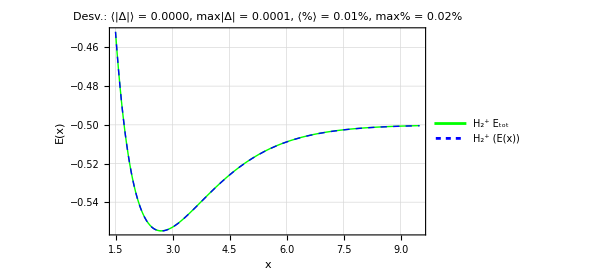
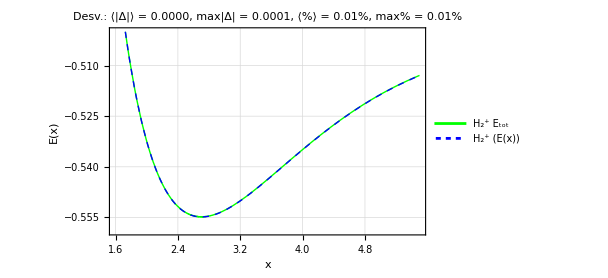
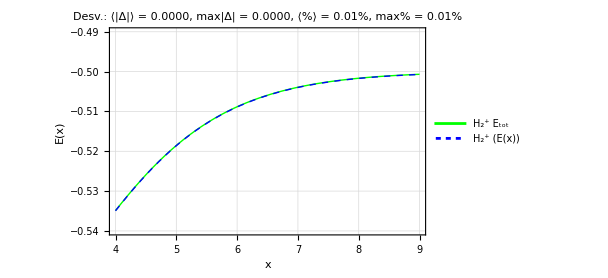
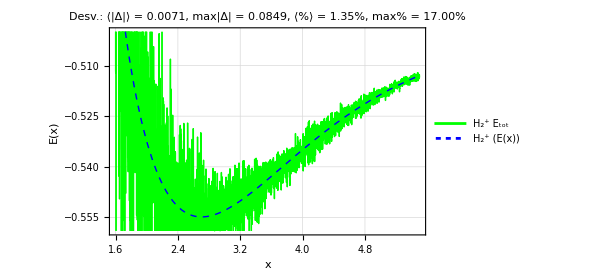
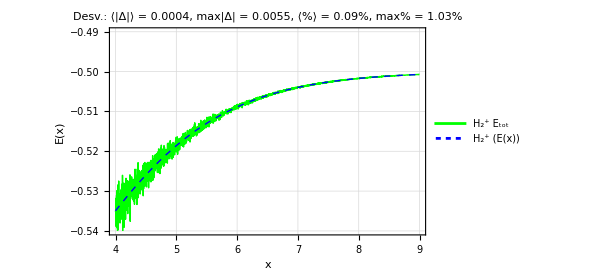
-Graphics-
Comparación global entre E_tot(x) y E(x) en un amplio rango de x, se muestra un buen acuerdo. | 
-Graphics-
Detalle de la región del mínimo de energía, la diferencia es sutil antes de R_e y notable después | -Graphics-
Vista amplida de la región de energía cercanas al límite asintótico (para x grande)
-Graphics-
Al aproximar Z_a=1 en E_tot(x) existe error de truncamiento, y empeora antes R_e... | -Graphics-
...como después de R_e, el ruido disminuye

```mathematica
(* ===utilidades===*)
ClearAll[devStats,makePanel];
devStats[f_,g_,{x_,xmin_,xmax_},step_:0.01]:=Module[{xs,valsF,valsG,dif,denom,rel},xs=N@Range[xmin,xmax,step];
valsF=f/@xs;
valsG=g/@xs;
dif=Abs[valsF-valsG];
denom=Clip[Abs[valsG],{10^-12,∞}];
rel=100 dif/denom;
<|"MeanAbs"->Mean[dif],"MaxAbs"->Max[dif],"MeanPct"->Mean[rel],"MaxPct"->Max[rel]|>];

(*makePanel ahora acepta Za (por defecto 0.9999), Zb y C1 (por defecto 1)*)
makePanel[{xmin_,xmax_},prange_,descripcion_,za_:0.9999,zb_:1,c1_:1]:=Module[{f=Function[{xx},Etot[xx,za,zb,c1]],g=Function[{xx},Ex[xx,zb,c1]],stats,plt},stats=devStats[f,g,{x,xmin,xmax}];
plt=Plot[{f[x],g[x]},{x,xmin,xmax},PlotRange->prange,AxesLabel->{"x","E(x)"},PlotStyle->{{Thick,Green},{Thick,Blue,Dashing[{0.01}]}},GridLines->Automatic,Frame->True,ImageSize->450,PlotLegends->{"H_2^+ E_tot","H_2^+ (E(x))"},PlotLabel->Style[Row[{"Desv.: ⟨|Δ|⟩ = ",NumberForm[stats["MeanAbs"],{6,4}],",  max|Δ| = ",NumberForm[stats["MaxAbs"],{6,4}],",  ⟨%⟩ = ",NumberForm[stats["MeanPct"],{5,2}],"%,  max% = ",NumberForm[stats["MaxPct"],{5,2}],"%"}],12,Bold]];
Column[{plt,Style[descripcion,Italic,11]},Spacings->{0.8,1.2}]];

(* ===disposición de las gráficas (ahora 5 paneles)===*)
Grid[{{makePanel[{1.5,9.5},All,"Comparación global entre E_tot(x) y E(x) en un amplio rango de x, se muestra un buen acuerdo."]},{makePanel[{1.6,5.5},{-0.559,-0.50},"Detalle de la región del mínimo de energía, la diferencia es sutil antes de R_e y notable después"],makePanel[{4.0,9.0},{-0.54,-0.49},"Vista amplida de la región de energía cercanas al límite asintótico (para x grande)"]},(*nuevas dos con Za=0.99999*){makePanel[{1.6,5.5},{-0.559,-0.50},"Al aproximar Z_a=1 en E_tot(x) existe error de truncamiento, y empeora antes R_e...",0.99999],makePanel[{4.0,9.0},{-0.54,-0.49},"...como después de R_e, el ruido disminuye",0.99999]}},Spacings->{2,2}]
```

#### Sobre los encabezados:

|Δ| → Media absoluta de la diferencia |E_tot-E(x)|. Da una idea del promedio de la discrepancia en las unidades de energía de tu cálculo.
max|Δ|→ Valor máximo absoluto de la diferencia en el intervalo de x que se está graficando.
⟨%⟩ → porcentaje promedio de la desviación relativa respecto a E(x). Es decir, (|E_tot-E(x)|)/(|E(x)|)×100 promediado sobre todos los puntos.
max% → porcentaje relativo máximo de desviación en el rango.
Lo anterior sirve para cuantificar qué tan bien coinciden ambas curvas en escala absoluta y relativa; e.g. si ⟨%⟩  es pequeño, ambas son prácticamente indistinguibles en promedio.

#### Generar tabla de valores numéricos para E_tot en formato .dat

```mathematica
datos=Table[{x,Etot[x,1,0.9999,1]},{x,1,10,0.1}]
Export["C:\\Users\\E_Joe\\Downloads\\Etot.dat",datos,"Table"];
```

{{1.,-0.189256},{1.1,-0.270161},{1.2,-0.332775},{1.3,-0.382245},{1.4,-0.42097},{1.5,-0.451805},{1.6,-0.476359},{1.7,-0.495704},{1.8,-0.510983},{1.9,-0.523066},{2.,-0.532383},{2.1,-0.53964},{2.2,-0.545048},{2.3,-0.548993},{2.4,-0.551769},{2.5,-0.553538},{2.6,-0.554517},{2.7,-0.554809},{2.8,-0.554588},{2.9,-0.553899},{3.,-0.5529},{3.1,-0.551599},{3.2,-0.550076},{3.3,-0.548393},{3.4,-0.546598},{3.5,-0.544709},{3.6,-0.542768},{3.7,-0.540794},{3.8,-0.538819},{3.9,-0.53685},{4.,-0.534905},{4.1,-0.532997},{4.2,-0.531138},{4.3,-0.52933},{4.4,-0.527584},{4.5,-0.525904},{4.6,-0.524291},{4.7,-0.522752},{4.8,-0.521277},{4.9,-0.519878},{5.,-0.518549},{5.1,-0.51729},{5.2,-0.516103},{5.3,-0.514981},{5.4,-0.513925},{5.5,-0.512931},{5.6,-0.511999},{5.7,-0.511127},{5.8,-0.510308},{5.9,-0.509543},{6.,-0.50883},{6.1,-0.508164},{6.2,-0.507543},{6.3,-0.506966},{6.4,-0.506429},{6.5,-0.50593},{6.6,-0.505467},{6.7,-0.505037},{6.8,-0.504639},{6.9,-0.50427},{7.,-0.503929},{7.1,-0.503613},{7.2,-0.503321},{7.3,-0.503051},{7.4,-0.502802},{7.5,-0.502572},{7.6,-0.50236},{7.7,-0.502165},{7.8,-0.501984},{7.9,-0.501818},{8.,-0.501665},{8.1,-0.501525},{8.2,-0.501395},{8.3,-0.501276},{8.4,-0.501166},{8.5,-0.501066},{8.6,-0.500973},{8.7,-0.500888},{8.8,-0.50081},{8.9,-0.500738},{9.,-0.500672},{9.1,-0.500612},{9.2,-0.500557},{9.3,-0.500506},{9.4,-0.500459},{9.5,-0.500416},{9.6,-0.500377},{9.7,-0.500341},{9.8,-0.500308},{9.9,-0.500278},{10.,-0.50025}}

Útil para llamar el archivo .dat desde Gnuplot y comenzar el ajuste para hallar “a” del Potencial de Morse.

#### Espectro rotacional y vibracional de H_2^+

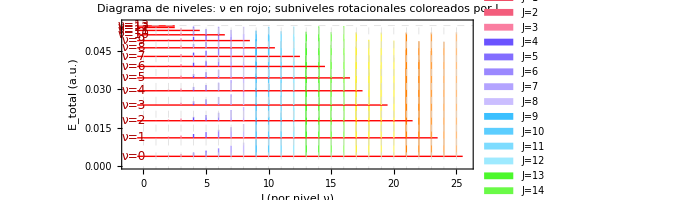

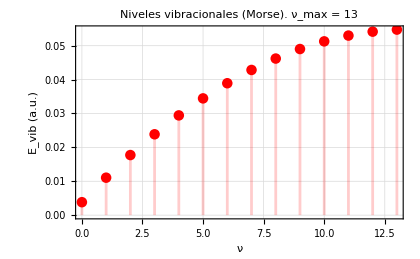
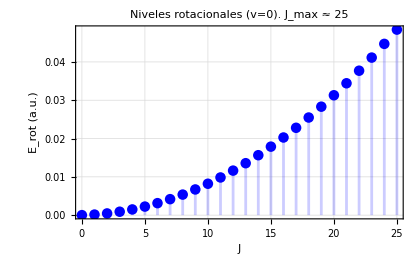
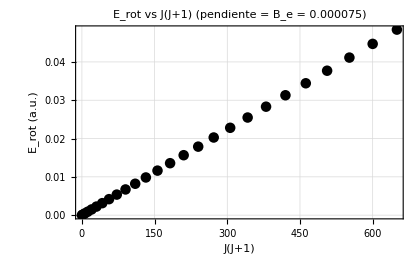
Constantes espectroscópicas útiles (a.u.)
ω_e | 0.007784
B_e = 1/(2  μ SubsuperscriptBox[R, e, 2]) | 0.000075
ν_max (Morse) | 13

-Graphics--Graphics-

-Graphics-

```mathematica
(* =====Constantes =====*)
hbar=1.;
mu=918.;
EB=0.0548486;      (*Subscript[D, e] en a.u.*)
Xmin=2.7035909800045945;   (*Subscript[R, e] en a.u.*)
a=0.712042;        (*en 1/(a.u.)*)

(* =====Frecuencia natural (a.u.)=====*)
omega0=a*Sqrt[(2*EB)/mu];
(* =====Energía vibracional (Morse)=====*)
Evib[nu_]:=omega0*(nu+1/2)-(omega0^2*(nu+1/2)^2)/(4*EB);
(* =====Energía rotacional (rotor rígido)=====*)
Erot[J_]:=(J*(J+1))/(2*mu*Xmin^2);
(* =====Constante rotacional en el mínimo=====*)
Be=1/(2*mu*Xmin^2);   (*a.u.;Erot[J]=Be*J(J+1)*)
(* =====Límites físicos=====*)
lambda=Sqrt[2*mu*EB]/a;              (*parámetro de Morse*)
nuMax=Floor[lambda-1/2];           (*último nivel ligado de vibración*)

(*Para cada v,tope rotacional antes de disociar:Evib[v]+Erot[J]<EB*)
Jmax[v_Integer?NonNegative]:=Module[{delta=EB-Evib[v]},If[delta<=0,-1,Floor[(-1+Sqrt[1+8*mu*Xmin^2*delta])/2]]];

(* =====1) Gráfica de niveles vibracionales=====*)
vibRange=Range[0,Max[0,nuMax]];
vibPlot=DiscretePlot[Evib[nu],{nu,vibRange[[1]],vibRange[[-1]]},PlotStyle->{Red,PointSize[0.018]},Filling->Axis,Frame->True,FrameLabel->{"ν","E_vib (a.u.)"},PlotLabel->Row[{"Niveles vibracionales (Morse).  ν_max = ",nuMax}],GridLines->{Automatic,Automatic},ImageSize->420];

(* =====2) Gráfica de niveles rotacionales (usar J(J+1) y J)=====*)
rotJmax=Max[0,Jmax[0]];   (*para v=0 como referencia*)
rotPlotJ=DiscretePlot[Erot[J],{J,0,Max[10,rotJmax]},PlotStyle->{Blue,PointSize[0.018]},Filling->Axis,Frame->True,FrameLabel->{"J","E_rot (a.u.)"},PlotLabel->Row[{"Niveles rotacionales (v=0).  J_max ≈ ",rotJmax}],GridLines->{Automatic,Automatic},ImageSize->420];

(*Linealidad en J(J+1):*)
rotPlotJJ1=ListPlot[Table[{J (J+1),Erot[J]},{J,0,Max[10,rotJmax]}],PlotStyle->{Black,PointSize[0.018]},Frame->True,FrameLabel->{"J(J+1)","E_rot (a.u.)"},PlotLabel->Row[{"E_rot vs J(J+1) (pendiente = B_e = ",NumberForm[Be,{6,6}],")"}],GridLines->{Automatic,Automatic},ImageSize->420];

(* =====3) Diagrama 2D:vibración+subniveles rotacionales=====*)
(* ===Colores por subnivel rotacional J (constantes en todos los ν)===*)
jMaxGlobal=Max[0,Max[Table[Jmax[v],{v,vibRange}]]];
paleta=ColorData["BrightBands"];           (*puedes probar "Rainbow" si prefieres*)
jColor[j_]:=paleta[Rescale[j,{0,jMaxGlobal}]];
leyendaJ=SwatchLegend[Table[jColor[j],{j,0,jMaxGlobal}],Table["J="<>ToString[j],{j,0,jMaxGlobal}]];
Legended[levelGraphics,Placed[leyendaJ,Right]]

(* ===Diagrama vibro-rotacional con color por J===*)
levelGraphics=Module[{rows},rows=Table[With[{Ev=Evib[v],jmax=Jmax[v]},{{Thick,Red,Line[{{-0.5,Ev},{Max[2,jmax]+0.5,Ev}}]},(*nivel vibracional ν*)Table[{jColor[j],Thick,Line[{{j,Ev},{j,Ev+Erot[j]}}]},(*subnivel rotacional J en color*){j,0,Max[0,jmax]}],Inset[Style["ν="<>ToString[v],12,Darker[Red]],{-0.8,Ev}]}],{v,vibRange}];
Graphics[{rows},Frame->True,FrameLabel->{"J (por nivel ν)","E_total (a.u.)"},PlotRange->{{-1.2,jMaxGlobal+0.8},{0,EB*1.02}},GridLines->{Range[0,jMaxGlobal,1],{EB}},GridLinesStyle->Directive[GrayLevel[.85],Dashed],PlotLabel->"Diagrama de niveles: ν en rojo; subniveles rotacionales coloreados por J",ImageSize->520]];


(* ===Mostrar===*)
Column[{Style["Constantes espectroscópicas útiles (a.u.)",14,Bold],Grid[{{"ω_e",NumberForm[omega0,{7,6}]},{"B_e = 1/(2  μ SubsuperscriptBox[R, e, 2])",NumberForm[Be,{7,6}]},{"ν_max (Morse)",nuMax}},Frame->All],Spacer[10],Row[{vibPlot,Spacer[20],rotPlotJ}],Spacer[10],rotPlotJJ1,Spacer[10]},Spacings->2]
```